## Topological Susceptibility χ interpolated from Borsanyi et al. 1606.07494

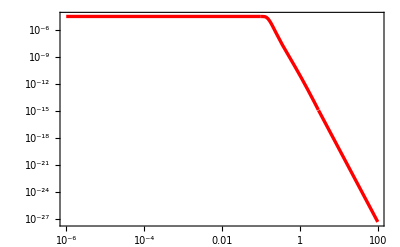

```mathematica
thick=Thickness[0.006];
χWUBU={{0.05,-4.488212193483247,-4.4997549464332,-4.4767456308768345},{0.12,-4.507770763968905,-4.437770763968905,-4.577770763968905},{0.14,-4.6077707639689045,-4.517770763968905,-4.697770763968905},{0.17,-5.037770763968905,-4.987770763968905,-5.087770763968905},{0.2,-5.577770763968905,-5.517770763968905,-5.637770763968906},{0.24,-6.247770763968905,-6.187770763968905,-6.307770763968906},{0.29,-6.967770763968906,-6.907770763968905,-7.027770763968904},{0.35000000000000003,-7.597770763968905,-7.537770763968906,-7.657770763968905},{0.42,-8.197770763968904,-8.127770763968904,-8.267770763968905},{0.5,-8.757770763968905,-8.677770763968905,-8.837770763968905},{0.6,-9.347770763968905,-9.257770763968905,-9.437770763968905},{0.72,-9.937770763968905,-9.827770763968905,-10.047770763968906},{0.86,-10.527770763968904,-10.397770763968905,-10.657770763968905},{1.,-11.027770763968904,-10.877770763968904,-11.177770763968905},{1.2,-11.647770763968904,-11.477770763968904,-11.817770763968904},{1.5,-12.417770763968905,-12.217770763968906,-12.617770763968904},{1.8,-13.057770763968904,-12.827770763968903,-13.287770763968904},{2.1,-13.607770763968905,-13.347770763968905,-13.867770763968904},{2.5,-14.237770763968905,-13.957770763968906,-14.517770763968905},{3.,-14.907770763968905,-14.577770763968905,-15.237770763968905}};
moss=Interpolation[χWUBU[[All,{1,2}]]];
WUBU[TGeV_]:=Piecewise[{{10^χWUBU[[1,2]],TGeV≤0.1},{10^moss[TGeV],0.1<TGeV≤3},{10^χWUBU[[-1,2]](TGeV/χWUBU[[-1,1]])^-8.16,TGeV>3}}];
LogLogPlot[WUBU[TGeV],{TGeV,10^-6,10^2},PlotStyle->{Red,thick},Frame->True]
```

## Defining the constants and the degrees of freedom

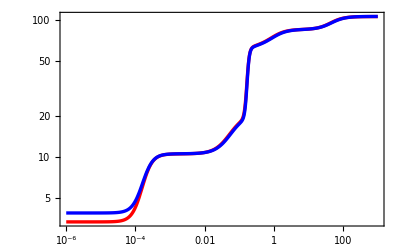

```mathematica
GeV=1;
s=1;
aR1={0.572,0.330,0.579,0.138,0.108};
aR2={-8.77,-2.95,-1.80,-0.162,3.76};
aR3={0.682,1.01,0.165,0.934,0.869};
aS1={0.498,0.327,0.579,0.14,0.109};
aS2={-8.74,-2.89,-1.79,-0.102,3.82};
aS3={0.693,1.01,0.155,0.963,0.907};
gsR[T_]:=Exp[1.21+Sum[aR1[[j]](1+Tanh[(Log10[T/GeV] Log[10]-aR2[[j]])/aR3[[j]]]),{j,1,5}]];
gsS[T_]:=Exp[1.36+Sum[aS1[[j]](1+Tanh[(Log10[T/GeV] Log[10]-aS2[[j]])/aS3[[j]]]),{j,1,5}]];
LogLogPlot[{gsR[t],gsS[t]},{t,10^-6,10^3},Frame->True,Axes->False,PlotStyle->{{Red,thick},{Blue,thick}}]
ϵ=10^-10;
tM=10^15;
tT=10^Range[Log10[ϵ],Log10[tM],0.1];
Nt=Length[tT];
ρRT[T_]:=π^2/30 gsR[T] T^4;
Hstd[T_]:=√(π^2/90 gsR[T])T^2/MPl;
HKN[T_,TR_]:=Piecewise[{{√(π^2/90 gsR[T])T^2/MPl,T≤TR},{√(π^2/90 gsR[T])T^3/(TR MPl),T>TR}}];
HLR[T_,TR_]:=Piecewise[{{√(π^2/90 gsR[T])T^2/MPl,T≤TR},{√(π^2/90 gsR[T])T^4/(TR^2 MPl),T>TR}}];
as[T_,TR_]:=Piecewise[{{TR/T,T≤TR},{(TR/T)^(8/3),T>TR}}];
MPl=2.4355 10^18;
hbar =6.582 10^-25 GeV s;
H0=(68 10^3 hbar)/(3.086 10^22);
βPl=0.037;
Δ2R=2.215 10^-9;
Λa=(WUBU[0])^(1/4) GeV;
T0=2.36 10^-13 GeV;
ρc=9.9 10^-48 GeV^4;
ΩCDMh2=0.12;
```

## Axion Cold Dark Matter in the Standard Cosmology

```mathematica
(*Time as the independent variable*)
```

```mathematica
μ=10^-3.915 10^-9;
Tosc=T/.FindRoot[3Hstd[T]==μ(√WUBU[T])/Λa^2,{T,1.}];
tosc=1/(2Hstd[Tosc]);
TT=Table[0,{i,1,Nt}];
Do[TT[[i]]=T/.FindRoot[tT[[i]]tosc==1/(2Hstd[T]),{T,10^-7}],{i,1,Nt}];
TF=Interpolation[Table[{tT[[i]],Abs[TT[[i]]]},{i,1,Nt}]];
tF=15;
Tf=TF[tF];
sol=NDSolve[{θ''[t]/tosc^2+3Hstd[TF[t]] θ'[t]/tosc+μ^2 WUBU[TF[t]]/Λa^4 Sin[θ[t]]==0,θ[ϵ]==π/(√3),θ'[ϵ]==0},θ,{t,ϵ,tF}];
θs[t_]:=Evaluate[θ[t]/.sol];
ρa[t_]:=Λa^4/μ^2(1/(2 tosc^2)(θs'[t])^2+μ^2 WUBU[TF[t]]/Λa^4(1-Cos[θs[t]]));
LogLogPlot[(ρa[t] t^(3/2))/(√WUBU[TF[t]]),{t,10^-2,tF},Frame->True,PlotRange->All]
ρa[tF]/(ΩCDMh2 ρc)√(WUBU[T0]/WUBU[Tf])gsS[T0]/gsS[Tf](T0/Tf)^3
```

The function F[μ0, θ0] returns the present axion energy density for a given axion mass μ0 (in GeV) and a given initial value of the axion misalignment angle θ0.
The function FD[μ0, θ0] is the derivative of F[μ0, θ0] with respect to θ0

```mathematica
F[μ0_,θ0_]:=Quiet[First[Module[{μ=μ0,θi=θ0},{Tosc=T/.FindRoot[3Hstd[T]==μ(√WUBU[T])/Λa^2,{T,1.}];
tosc=1/(2Hstd[Tosc]);
TT=Table[0,{i,1,Nt}];
Do[TT[[i]]=T/.FindRoot[tT[[i]]tosc==1/(2Hstd[T]),{T,10^-7}],{i,1,Nt}];
TF=Interpolation[Table[{tT[[i]],Abs[TT[[i]]]},{i,1,Nt}]];
tF=15;
Tf=TF[tF];
eqAx=θ''[t]/tosc^2+3Hstd[TF[t]] θ'[t]/tosc+μ^2 WUBU[TF[t]]/Λa^4 Sin[θ[t]];
sol=NDSolve[{eqAx==0,θ[ϵ]==θi,θ'[ϵ]==0},θ,{t,ϵ,tF}];
θs[t_]:=Evaluate[θ[t]/.sol];
ρa[t_]:=Λa^4/μ^2(1/(2 tosc^2)(θs'[t])^2+μ^2 WUBU[TF[t]]/Λa^4(1-Cos[θs[t]]));
fA=ρa[tF]/(ΩCDMh2 ρc)√(WUBU[T0]/WUBU[Tf])gsS[T0]/gsS[Tf](T0/Tf)^3//First;
Return[fA];}]]];

FD[μ0_,θ0_]:=Module[{μ=μ0,θi=θ0},Return[(F[μ0,θ0(1+10^-3 (π-θ0))]-F[μ0,θ0])/(10^-3 (π-θ0))];];
```

Plotting θ0 as a function of the axion mass.
Scenario in which the Peccei-Quinn symmetry breaks during inflation and it is not restored afterwards;
Isocurvature bounds give the upper bound on the Hubble rate at the end of inflation H_I

```mathematica
θT=Join[π-10^Range[-4,-2,0.1],10^Range[Log10[π-0.1],-3.5+Log10[π-0.1],-0.1]];
θT=10^Range[Log10[π-0.1],-3.5+Log10[π-0.1],-0.2];
NG=Length[θT];
mT=Table[0,{i,1,NG}];
HIT=Table[0,{i,1,NG}];
```

```mathematica
Do[{θ0=θT [[i]];
μA=10^-2 10^-9;
μB=10^-10 10^-9;
ρA=F[μA,θ0];
ρB=F[μB,θ0];
μC=√(μA μB);
ρC=F[μC,θ0];
(*tolerence*)
eps=0.005;
count=0;
countvalve=100;
While[Abs[ρC-1]>eps,
count=count+1;
μC=(μA μB)^0.5;
ρC=F[μC,θ0];
If[ρC<1,{μA=μC,ρA=ρC},{μB=μC,ρB=ρC}];
If[count>countvalve,Break[]];];
mT[[i]]=μC;Print[i];},{i,1,NG}];
```

```mathematica
ListLinePlot[Table[{Log10[Sort[10^9 mT,Greater][[i]]],Sort[θT,Greater][[i]]},{i,1,NG}]]
```

```mathematica
Do[{HIT[[i]]=((2π Λa^2)/mT[[i]])Abs[F[mT[[i]],θT [[i]]]/FD[mT[[i]],θT [[i]]]] √((βPl Δ2R)/(1-βPl));Print[i];},{i,1,NG}]
```

```mathematica
ListLinePlot[Table[{Log10[Sort[HIT,Greater][[i]]],Log10[Sort[10^9 mT,Greater][[i]]]},{i,1,NG}]]
```

```mathematica
(*Temperature as the independent variable*)
```

```mathematica
(*Gives the same results as for the time variable*)
μ=10^-3.95 10^-9;
Tosc=T/.FindRoot[3Hstd[T]==μ(√WUBU[T])/Λa^2,{T,1.}];
F1[τ_]:=-1 -(τ1 D[gsS[Tosc τ1],τ1])/(3gsS[Tosc τ1])/.τ1->τ;
F2[τ_]:=τ1/2 D[gsR[Tosc τ1],τ1]/gsR[Tosc τ1]-(τ1^2 D[gsS[Tosc τ1],{τ1,2}]+4τ1 D[gsS[Tosc τ1],τ1])/(τ1 D[gsS[Tosc τ1],τ1] + 3gsS[Tosc τ1])/.τ1->τ;
τi=0.3;
τF=10^5;
Axsol=NDSolve[{θ''[τ]+F2[τ]/τ θ'[τ]+(F1[τ]/(τ Hstd[Tosc τ]))^2 μ^2 WUBU[Tosc τ]/Λa^4 Sin[θ[τ]]==0,θ[τF]==π/(√3),θ'[τF]==0},θ,{τ,τi,τF}];
θs[τ_]:=Evaluate[θ[τ]/.Axsol];
ρa[τ_]:=(1/2(-(2 Hstd[Tosc τ]^2)/(D[Hstd[Tosc τ1],τ1]/.τ1->τ)θs'[τ])^2+μ^2 WUBU[Tosc τ]/Λa^4(1-Cos[θs[τ]]))Λa^4/μ^2;
fCDM=ρa[τi]/(ΩCDMh2 ρc)√(WUBU[T0]/WUBU[τi Tosc])gsS[T0]/gsS[τi Tosc](T0/(τi Tosc))^3//First;
Print[fCDM];
```

1.06377

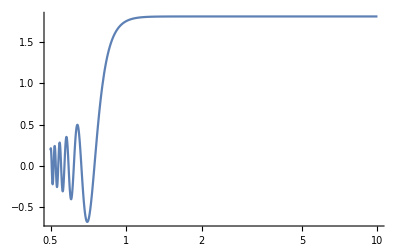

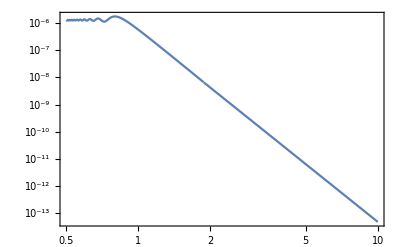

```mathematica
LogLinearPlot[θs[τ],{τ,0.5,10},PlotRange->All]
LogLogPlot[(ρa[τ] τ^-3)/(√WUBU[Tosc τ]),{τ,0.5,10},Frame->True]
```

```mathematica
dH/dT=α H/T
```

```mathematica
dT/dt=dT/dH dH/dt=(T H)/(α β)
```

## Axion Cold Dark Matter in Modified Cosmological histories

```mathematica
Solving  (dT/dt)^2 θ''+(3H(T)dT/dt+(d^2 T)/dt^2)θ'+m^2 θ = 0
A prime is a derivation with respect to temperature (in units of Subscript[T, osc])
During kination H(T) \sim T^3
During LRT H(T) \sim T^4
dT/dt and (d^2 T)/dt^2 are approximated by step functions that are smoothed out at reheating with a ArcTan function.
```

#### Axion CDM in LRT and kination cosmologies, Temperature variable

1.32791

1.32791

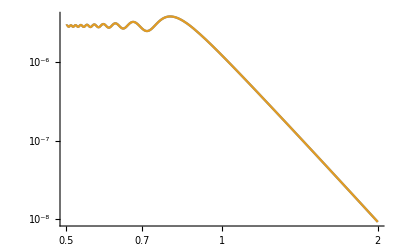

4.3341

4.32982

```mathematica
μ=10^-4.44 10^-9;
TRH=5;
ToscK=T/.FindRoot[3HKN[T,TRH]==μ(√WUBU[T])/Λa^2,{T,1.}];
ToscL=T/.FindRoot[3HLR[T,TRH]==μ(√WUBU[T])/Λa^2,{T,1.}];
Print[ToscK];
Print[ToscL];
τRHK=TRH/ToscK;
τRHL=TRH/ToscL;
F2K[τ_]:=Piecewise[{{1,τ>τRHK},{0,τ≤τRHK}}];
F1L[τ_]:=1+5/(3π)(π/2+ArcTan[(τ-τRHL)/0.002]);
F2L[τ_]:=-3+3/π(π/2-ArcTan[(τ-τRHL)/0.002]);
τi=0.5;
τF=10^5;
ω2K[τ_]:=(1/(τ HKN[ToscK τ,TRH]))^2 μ^2 WUBU[ToscK τ]/Λa^4;
ω2L[τ_]:=(F1L[τ]/(τ HLR[ToscL τ,TRH]))^2 μ^2 WUBU[ToscL τ]/Λa^4;
(* Equation of motion in each cosmological model *)
AxsolK=NDSolve[{θ''[τ]+F2K[τ]/τ θ'[τ]+ω2K[τ]Sin[θ[τ]]==0,θ[τF]==π/(√3),θ'[τF]==0},θ,{τ,τi,τF}];
AxsolL=NDSolve[{θ''[τ]+F2L[τ]/τ θ'[τ]+ω2L[τ]Sin[θ[τ]]==0,θ[τF]==π/(√3),θ'[τF]==0},θ,{τ,τi,τF}];
θK[τ_]:=Evaluate[θ[τ]/.AxsolK];
θL[τ_]:=Evaluate[θ[τ]/.AxsolL];
ρaK[τ_]:=(τ HKN[ToscK τ,TRH])^2(1/2 θK'[τ]^2+ω2K[τ](1-Cos[θK[τ]]))Λa^4/μ^2//First;
ρaL[τ_]:=((τ HLR[ToscL τ,TRH])/F1L[τ])^2(1/2 θL'[τ]^2+ω2L[τ](1-Cos[θL[τ]]))Λa^4/μ^2//First;
LogLogPlot[{(ρaK[τ] τ^-3)/(√WUBU[ToscK τ]),ρaL[τ]/(√WUBU[ToscL τ])as[ToscL τ,TRH]^3/as[ToscL,TRH]^3},{τ,τi,2}]

(*fK and fL are the fractions of energy densities in cold axions in the two cosmologies, over the total CDM energy density*)
fK=ρaK[τi]/(ΩCDMh2 ρc)√(WUBU[T0]/WUBU[ToscK τi])gsS[T0]/gsS[ToscK τi](T0/(ToscK τi))^3
fL =ρaL[τi]/(ΩCDMh2 ρc)√(WUBU[T0]/WUBU[ToscL τi])(as[ToscL τi,TRH]/as[ToscL τRHL,TRH])^3 gsS[T0]/gsS[ToscL τi](T0/TRH)^3
```

The function FLRT[μ0, θ0] returns the present axion energy density for a given axion mass μ0 (in GeV) and a given initial value of the axion misalignment angle θ0, in the LRT cosmology
The function FLRTD[μ0, θ0] is the derivative of FLRT[μ0, θ0] with respect to θ0

```mathematica
FLRT[μ0_,θ0_,TR_]:=Quiet[First[Module[{μ=μ0,θi=θ0,Trh=TR},{ToscL=T/.FindRoot[3HLR[T,Trh]==μ(√WUBU[T])/Λa^2,{T,1.}];
τRHL=Trh/ToscL;
F1L[τ_]:=1+5/(3π)(π/2+ArcTan[(τ-τRHL)/0.002]);
F2L[τ_]:=-3+3/π(π/2-ArcTan[(τ-τRHL)/0.002]);
τi=0.5;
τF=10^5;
ω2L[τ_]:=(F1L[τ]/(τ HLR[ToscL τ,Trh]))^2 μ^2 WUBU[ToscL τ]/Λa^4;
AxsolL=NDSolve[{θ''[τ]+F2L[τ]/τ θ'[τ]+ω2L[τ]Sin[θ[τ]]==0,θ[τF]==θi,θ'[τF]==0},θ,{τ,τi,τF}];
θL[τ_]:=Evaluate[θ[τ]/.AxsolL];
ρaL[τ_]:=((τ HLR[ToscL τ,Trh])/F1L[τ])^2(1/2 θL'[τ]^2+ω2L[τ](1-Cos[θL[τ]]))Λa^4/μ^2//First;fL =ρaL[τi]/(ΩCDMh2 ρc)√(WUBU[T0]/WUBU[ToscL τi])(as[ToscL τi,Trh]/as[ToscL τRHL,Trh])^3 gsS[T0]/gsS[ToscL τi](T0/Trh)^3;
Remove[AxsolL, τi,τF,F1L,F2L,ω2L,τRHL,ToscL];
Return[fL];}]]];

FLRTD[μ0_,θ0_]:=Module[{μ=μ0,θi=θ0},Return[(FLRT[μ0,θ0(1+10^-3 (π-θ0))]-FLRT[μ0,θ0])/(10^-3 (π-θ0))];];
```

The function FKIN[μ0, θ0] returns the present axion energy density for a given axion mass μ0 (in GeV) and a given initial value of the axion misalignment angle θ0, in the kination cosmology
The function FKIND[μ0, θ0] is the derivative of FKIN[μ0, θ0] with respect to θ0

```mathematica
FKIN[μ0_,θ0_,TR_]:=Quiet[First[Module[{μ=μ0,θi=θ0,Trh=TR},{ToscK=T/.FindRoot[3HKN[T,Trh]==μ(√WUBU[T])/Λa^2,{T,1.}];
τRH=Trh/ToscK;
F2K[τ_]:=Piecewise[{{1,τ>τRHK},{0,τ≤τRHK}}];
τi=0.5;
τF=10^5;
ω2[τ_]:=(1/(τ HKN[ToscK τ,Trh]))^2 μ^2 WUBU[ToscK τ]/Λa^4;
AxsolK=NDSolve[{θ''[τ]+F2K[τ] θ'[τ]/τ+ω2[τ]Sin[θ[τ]]==0,θ[τF]==θi,θ'[τF]==0},θ,{τ,τi,τF}];
θs[τ_]:=Evaluate[θ[τ]/.AxsolK];
ρaK[τ_]:=(τ HKN[ToscK τ,Trh])^2(1/2 θs'[τ]^2+ω2[τ](1-Cos[θs[τ]]))Λa^4/μ^2//First;
fK=ρaK[τi]/(ΩCDMh2 ρc)√(WUBU[T0]/WUBU[ToscK τi])gsS[T0]/gsS[ToscK τi](T0/(ToscK τi))^3;
Remove[AxsolK, τi,τF,F1K,F2K,ω2K,τRHK,ToscK];
Return[fK];}]]];

FKIND[μ0_,θ0_]:=Module[{μ=μ0,θi=θ0},Return[(FKIN[μ0,θ0(1+10^-3 (π-θ0))]-FKIN[μ0,θ0])/(10^-3 (π-θ0))];]
```

Bisection method to find the value of the axion mass that yields 100% of the CDM for a given reheat temperature in the LRT cosmology

```mathematica
TrhT=10^Range[-3,1.3,0.05];
NT=Length[TrhT];
mrhT=Table[0,{i,1,NT}];
mknT=Table[0,{i,1,NT}];
```

```mathematica
Do[{Trh=TrhT [[i]];
μA=10^-2 10^-9;
μB=10^-10 10^-9;
ρA=FLRT[μA,π/(√3),Trh];
ρB=FLRT[μB,π/(√3),Trh];
μC=√(μA μB);
ρC=FLRT[μC,π/(√3),Trh];
(*tolerence*)
eps=0.01;
count=0;
countvalve=100;
While[Abs[ρC-1]>eps,
count=count+1;
μC=(μA μB)^0.5;
ρC=FLRT[μC,π/(√3),Trh];
If[ρC<1,{μA=μC,ρA=ρC},{μB=μC,ρB=ρC}];
If[count>countvalve,Break[]];];
mrhT[[i]]=μC;
Print[i];},{i,1,NT}];
```

Bisection method to find the value of the axion mass that yields 100% of the CDM for a given reheat temperature in the kination cosmology

```mathematica
TknT=10^Range[-3,1,0.2];
NK=Length[TknT];
mknT=Table[0,{i,1,NK}];
```

```mathematica
Do[{Trh=TknT [[i]];
μA=10^-2 10^-9;
μB=10^-10 10^-9;
ρA=FKIN[μA,π/(√3),Trh];
ρB=FKIN[μB,π/(√3),Trh];
μC=√(μA μB);
ρC=FKIN[μC,π/(√3),Trh];
(*tolerence*)
eps=0.01;
count=0;
countvalve=100;
While[Abs[ρC-1]>eps,
count=count+1;
μC=(μA μB)^0.5;
ρC=FKIN[μC,π/(√3),Trh];
If[ρC<1,{μA=μC,ρA=ρC},{μB=μC,ρB=ρC}];
If[count>countvalve,Break[]];];
mknT[[i]]=μC;
Print[i];},{i,1,NK}];
```

```mathematica
PlotLRT=ListLinePlot[Table[{Log10[TrhT[[i]]],Log10[10^9 mrhT[[i]]]},{i,1,NT}],PlotStyle->{Blue,thick}];
PlotKIN=ListLinePlot[Table[{Log10[TknT[[i]]],Log10[10^9 mknT[[i]]]},{i,1,NK}],PlotStyle->{Red,thick}];
Show[PlotLRT,PlotKIN,PlotRange->All]
```

## Finding the background by coupled Boltzmann equations

```mathematica
ρψ0=10^24 GeV^4;
ρR0=0;
ω=0;
ϵ=10^-10;
eqa=a'[t]-a[t] √(ρR[t]+ρψ0 a[t]^(-3(1+ω))Exp[-t]);
eqψ=ρψ'[t]+3 a'[t]/a[t](1+ω) ρψ[t]+ρψ[t];
eqR=ρR'[t]+4 a'[t]/a[t] ρR[t]-ρψ0 a[t]^(-3(1+ω))Exp[-t];
solB=NDSolve[{eqR==0,eqa==1,ρR[ϵ]==ρR0,a[ϵ]==1},{ρR,a},{t,ϵ,tM}];
aa[t_]:=Evaluate[Abs[a[t]]/.solB]//First;
ha[t_]:=Evaluate[Abs[a'[t]/a[t]]/.solB]//First;
haD[t_]:=Evaluate[a''[t]/a[t]-(a'[t]/a[t])^2/.solB]//First;
rRa[t_]:=Evaluate[Abs[ρR[t]]/.solB]//First;
rψa[t_]:=ρψ0 aa[t]^(-3(1+ω))Exp[-t];
tRH=t/.FindRoot[rψa[t]==rRa[t],{t,ϵ}];
(*Clear[aa];
aa[t_]:=Evaluate[Abs[a[t]/a[tRH]]/.sol]//First;*)
Print[tRH];
rRH=rRa[tRH];
```

1.0538

0.00958826

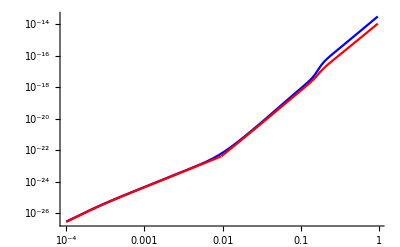

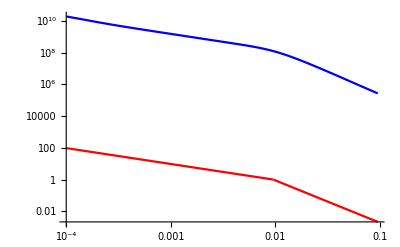

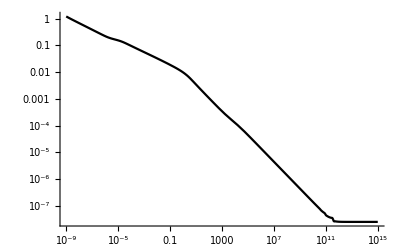

```mathematica
Γ=10^-22 GeV;
ρI=3 Γ^2 MPl^2 GeV^4;
iM=1;
II=9 +Log10[10^17 Γ];
While[tT[[iM]]<10^-9,iM=iM+1];
TT=Table[0,{i,1,Nt}];
Do[TT[[i]]=T/.FindRoot[ρRT[T]==ρI rRa[tT[[i]]],{T,10.}],{i,1,Nt}];
TF=Interpolation[Table[{tT[[i]],TT[[i]]},{i,1,Nt}]];
tf=Interpolation[Table[{TT[[i]],tT[[i]]/tRH},{i,iM,Nt}]];
TRH=TF[tRH];
Print[TRH];
H[T_]:=Γ ha[tf[T]];
HD[T_]:=Γ haD[t]D[tf[T1],T1]/.t->tf[T1]/.T1->T;
HRH=Γ ha[tRH];
LogLogPlot[{H[T],HLR[T,TRH]},{T,10^-4,100TRH},PlotStyle->{Blue,Red}]
LogLogPlot[{aa[tf[T]],as[T,TRH]},{T,10^-4,10 TRH},PlotStyle->{Blue,Red}]
LogLogPlot[TF[t],{t,tT[[iM]],tM},PlotStyle->Black]
```

InterpolatingFunction::dmval: Input value {1.46269} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.4632} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.46327} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

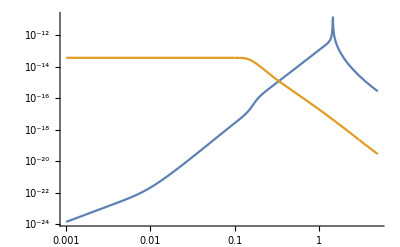

0.334177

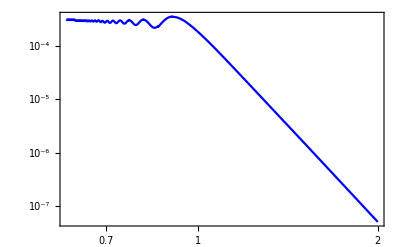

0.000313225

```mathematica
μ=10^-4.44 10^-9;
Tosc=T/.FindRoot[3H[T]==μ(√WUBU[T])/Λa^2,{T,1.}];
LogLogPlot[{3H[T],μ(√WUBU[T])/Λa^2},{T,0.001,5}]
as[τ_]:=aa[tf[Tosc τ]];
τRH=TRH/Tosc;
TFD[τ_]:=TF'[tt]/.tt->tf[Tosc τ];
TFDD[τ_]:=TF''[tt]/.tt->tf[Tosc τ];
ω2[τ_]:=(Tosc/(Γ TFD[τ]))^2 μ^2 WUBU[Tosc τ]/Λa^4;
(*ωF2[τ_]:=((tf[T] HD[T])/(Γ H[T]))^2 μ^2/Tosc^2 WUBU[T]/Λa^4/.T->Tosc τ;*)
Print[Tosc];
TFD[τ_]:=TF'[tt]/.tt->tf[Tosc τ];
TFDD[τ_]:=TF''[tt]/.tt->tf[Tosc τ];
F1[τ_]:=Piecewise[{{(tf[T] HD[T] T)/Γ/.T->Tosc τ,τ>τRH},{-1,τ<τRH}}];
F2[τ_]:=Piecewise[{{Tosc(1/TFD[τ])^2(3 H[Tosc τ]/Γ TFD[τ]+TFDD[τ]),τ>τRH},{0,τ<τRH}}];
τi=0.6;
τF=2;
Axsol=NDSolve[{θ''[τ]+F2[τ]θ'[τ]+ω2[τ]Sin[θ[τ]]==0,θ[τF]==π/(√3),θ'[τF]==0},θ,{τ,τi,τF}];
θs[τ_]:=Evaluate[θ[τ]/.Axsol];
ρas[τ_]:=1/(ΩCDMh2 ρc)((Γ TFD[τ])/Tosc)^2(1/2 θs'[τ]^2+ω2[τ](1-Cos[θs[τ]]))Λa^4/μ^2 √(WUBU[T0]/WUBU[Tosc τ])(aa[tf[Tosc τ]]/aa[tf[TRH]])^3 gsS[T0]/gsS[TRH](T0/TRH)^3//First;
fA=ρas[τi];
LogLogPlot[{ρas[τ]},{τ,τi,2},Frame->True,PlotStyle->{Blue}]
Print[fA];
Remove[Axsol];
```

```mathematica
FBOL[μ0_,θ0_,Γ0_]:=Quiet[First[Module[{μ=μ0,θi=θ0,γ=Γ0},{
ρI=3 γ^2 MPl^2 GeV^4;
iM=1;
II=9 +Log10[10^17 γ];
While[tT[[iM]]<10^-9,iM=iM+1];
TT=Table[0,{i,1,Nt}];
Do[TT[[i]]=T/.FindRoot[ρRT[T]==ρI rRa[tT[[i]]],{T,10.}],{i,1,Nt}];
TF=Interpolation[Table[{tT[[i]],TT[[i]]},{i,1,Nt}]];
tf=Interpolation[Table[{TT[[i]],tT[[i]]/tRH},{i,iM,Nt}]];
TRH=TF[tRH];
H[T_]:=γ ha[tf[T]];
HD[T_]:=γ haD[t]D[tf[T1],T1]/.t->tf[T1]/.T1->T;
HRH=γ ha[tRH];
Tosc=T/.FindRoot[3H[T]==μ(√WUBU[T])/Λa^2,{T,1.}];
as[τ_]:=aa[tf[Tosc τ]];
τRH=TRH/Tosc;
TFD[τ_]:=TF'[tt]/.tt->tf[Tosc τ];
TFDD[τ_]:=TF''[tt]/.tt->tf[Tosc τ];
ω2[τ_]:=(Tosc/(γ TFD[τ]))^2 μ^2 WUBU[Tosc τ]/Λa^4;
TFD[τ_]:=TF'[tt]/.tt->tf[Tosc τ];
TFDD[τ_]:=TF''[tt]/.tt->tf[Tosc τ];
F1[τ_]:=Piecewise[{{(tf[T] HD[T] T)/γ/.T->Tosc τ,τ>τRH},{-1,τ<τRH}}];
F2[τ_]:=Piecewise[{{Tosc(1/TFD[τ])^2(3 H[Tosc τ]/γ TFD[τ]+TFDD[τ]),τ>τRH},{0,τ<τRH}}];
τi=0.6;
τF=2;
Axsol=NDSolve[{θ''[τ]+F2[τ]θ'[τ]+ω2[τ]Sin[θ[τ]]==0,θ[τF]==θi,θ'[τF]==0},θ,{τ,τi,τF}];
θs[τ_]:=Evaluate[θ[τ]/.Axsol];
ρas[τ_]:=1/(ΩCDMh2 ρc)((γ TFD[τ])/Tosc)^2(1/2 θs'[τ]^2+ω2[τ](1-Cos[θs[τ]]))Λa^4/μ^2 √(WUBU[T0]/WUBU[Tosc τ])(aa[tf[Tosc τ]]/aa[tf[TRH]])^3 gsS[T0]/gsS[TRH](T0/TRH)^3//First;
Return[{TRH,ρas[τi]}];
Remove[Axsol, τi,τF,F1,F2,ω2,τRH,Tosc];}]]]
```

```mathematica
ΓT=10^Range[-22,-16,0.5];
NT=Length[ΓT];
mrhT=Table[0,{i,1,NT}];
TrhT=Table[0,{i,1,NT}];
```

```mathematica
Do[{γ0=ΓT[[i]];
μA=10^-2 10^-9;
μB=10^-10 10^-9;
ρA=FBOL[μA,π/(√3),γ0][[2]];
ρB=FBOL[μB,π/(√3),γ0][[2]];
μC=√(μA μB);
sol=FBOL[μC,π/(√3),γ0];
trh=sol[[1]];
ρC=sol[[2]];
(*tolerence*)
eps=0.01;
count=0;
countvalve=100;
While[Abs[ρC-1]>eps,
count=count+1;
μC=(μA μB)^0.5;
sol=FBOL[μC,π/(√3),γ0];
trh=sol[[1]];
ρC=sol[[2]];
If[ρC<1,{μA=μC,ρA=ρC},{μB=μC,ρB=ρC}];
If[count>countvalve,Break[]];];
mrhT[[i]]=μC;
TrhT[[i]]=trh;
Print[i];},{i,1,NT}];
```

1

2

3

4

5

6

7

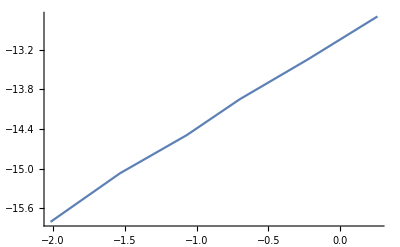

```mathematica
ListLinePlot[Table[{Log10[TrhT[[i]]],Log10[mrhT[[i]]]},{i,1,NT}]]
```